```mathematica
f[t_]:=Abs[Cos[4t]] + Sin[t] 

n=7;
h=-π;
T=4 π;

A[i_]:=(2/T) Integrate[f[t] Cos[(2 Pi i t)/T],{t,h,h+T}];
B[i_]:=(2/T) Integrate[f[t] Sin[(2 Pi i t)/T],{t,h,h+T}];

Cc[i_]:=(1/T) Integrate[f[t] Exp[-I (2 Pi i t)/T],{t,h,h+T}];

rad=A[0]/2;
For[i=1,i≤n,i++,Print["A[",i,"] = ",A[i],"  B[",i,"] = ",B[i]];
rad=rad+A[i] Cos[(2 Pi i t)/T]+B[i] Sin[(2 Pi i t)/T];]

For[i=-n,i≤n,i++,Print["Cc[",i,"] = ",Re[Cc[i]]," + I * ",Im[Cc[i]]];]

radComplex=Sum[Re[Cc[i]] Cos[(2 Pi i t)/T]-Im[Cc[i]] Sin[(2 Pi i t)/T],{i,-n,n}];

Plot[{rad,radComplex,f[t]},{t,h,h+T},PlotStyle->{{Thick,Blue},{Thick,Dashed,Red},{Thick,Green}},AxesLabel->{"t","y"},PlotRange->All,PlotLegends->{"Реальный ряд Фурье","Комплексный ряд Фурье","Исходная функция"}]

N[rad]
N[radComplex]

Plot[f[t],{t, h,h+T},PlotStyle->{Thick,Blue},AxesLabel->{"t","y"},PlotRange->All,PlotLegends->{"Исходная функция"}]
```

A[1] = (-5 Cos[π/16]+4 Cos[π/16]^3-Cos[(3 π)/16]-3 Sin[π/16]+4 Sin[π/16]^3+7 Sin[(3 π)/16]-8 Sin[(3 π)/16]^3)/(6 π)  B[1] = (-5 Cos[π/16]+4 Cos[π/16]^3-Cos[(3 π)/16]-3 Sin[π/16]+4 Sin[π/16]^3+7 Sin[(3 π)/16]-8 Sin[(3 π)/16]^3)/(6 π)

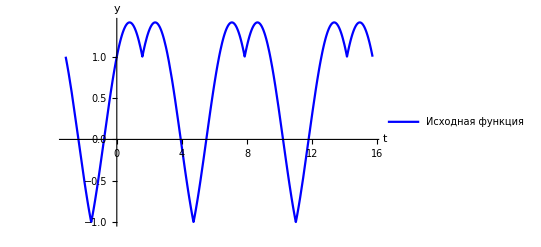

2. Sin[t]-1. Sin[2. t]+1.66667 Sin[3. t]-0.5 Sin[4. t]+0.4 Sin[5. t]-0.333333 Sin[6. t]+0.285714 Sin[7. t]-0.25 Sin[8. t]+0.222222 Sin[9. t]-0.2 Sin[10. t]

2. Sin[t]-1. Sin[2. t]+1.66667 Sin[3. t]-0.5 Sin[4. t]+0.4 Sin[5. t]-0.333333 Sin[6. t]+0.285714 Sin[7. t]-0.25 Sin[8. t]+0.222222 Sin[9. t]-0.2 Sin[10. t]

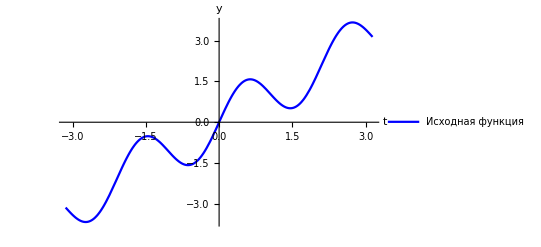

```mathematica
0.6366197723675814+Sin[t]
```

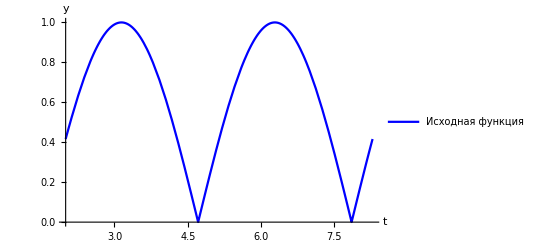

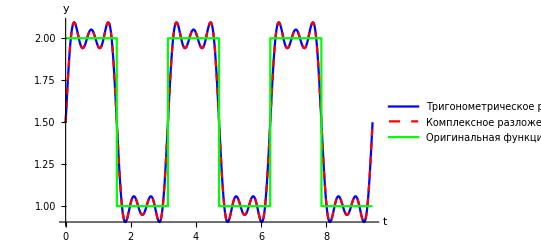

```mathematica
a=2;
b=1;
t0=0;
t1=Pi/2;
t2=Pi;
T=t2-t0;
h=3;

f[t_]:=Piecewise[{{a,0≤Mod[t,T]≤t1},{b,t1<Mod[t,T]≤t2}}];

n=5;

A0=(2/T) Integrate[f[t],{t,0,T}];

A[k_]:=(2/T) Integrate[f[t] Cos[(2 Pi k t)/T],{t,0,T}];
B[k_]:=(2/T) Integrate[f[t] Sin[(2 Pi k t)/T],{t,0,T}];

A0val=N[A0];
Avals=Table[N[A[k]],{k,1,n}];
Bvals=Table[N[B[k]],{k,1,n}];

fourierSeries=A0val/2+Sum[Avals[[k]] Cos[(2 Pi k t)/T]+Bvals[[k]] Sin[(2 Pi k t)/T],{k,1,n}];

c[n_]:=(1/T) Integrate[f[t] Exp[-I (2 Pi n t)/T],{t,0,T}];

cVals=Table[N[c[k]],{k,-n,n}];

fourierSeriesComplex=A0val/2+2 Sum[Re[cVals[[k+n+1]]] Cos[(2 Pi k t)/T]-Im[cVals[[k+n+1]]] Sin[(2 Pi k t)/T],{k,1,n}];

Plot[{fourierSeries,fourierSeriesComplex,f[t]},{t,0,3*T},PlotStyle->{{Thick,Blue},{Thick,Dashed,Red},{Thick,Green}},PlotLegends->{"Тригонометрическое разложение (A + B)","Комплексное разложение (c_n)","Оригинальная функция"},AxesLabel->{"t","y"},PlotRange->All,Exclusions->None]
```